```mathematica
<<MaTeX`
```

```mathematica
F[x_, a_]:= Piecewise[{{(x (2-x))^a, 0  <= x  <= 1}},0]
```

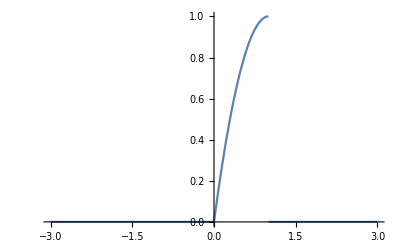

```mathematica
Plot[ F[x,1],{x,-3,3}]
```

```mathematica
delta[x_, lambda_, p_] :=Piecewise[{{x F[1- (lambda/Abs[x])^p , 1], Abs[x]>lambda}},0]
```

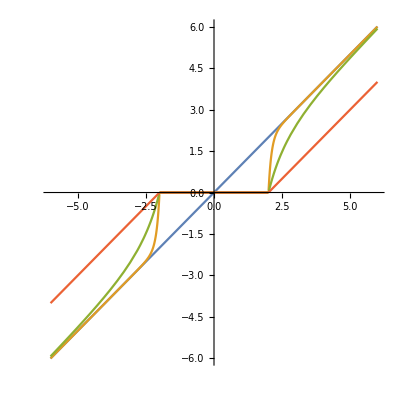

```mathematica
Plot[{x,delta[x, 2, 10], delta[x,2,2], delta[x,2,0.5]},{x,-6,6}, AspectRatio -> Automatic,AxesLabel->{MaTeX["x"],MaTeX["y"]},TicksStyle->Directive[FontFamily->"Roman",FontSlant->"Plain",11],
PlotStyle->{Directive[Black,Dotted,Thickness[0.003]],Directive[Black,Thick],Directive[Black,Thick],Directive[Black,Thick]}.
PlotLegends-> Placed[{Style["y = x",14],
Style["p=10",14], Style["p=2",14],
Style["p=1",14]}, Above]
]
```

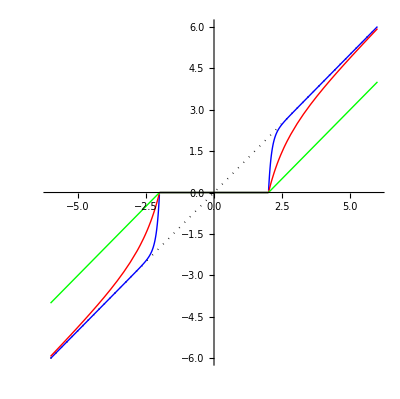

```mathematica
Plot[{x,delta[x,2,10],delta[x,2,2],delta[x,2,0.5]},{x,-6,6},AspectRatio->Automatic,AxesLabel->{MaTeX["x"],MaTeX["y"]},TicksStyle->Directive[FontFamily->"Roman",FontSlant->"Plain",11],PlotStyle->{Directive[Black,Dotted,Thickness[0.003]],Directive[Blue,Thick],Directive[Red,Thick],Directive[Green,Thick]},PlotLegends->Placed[Framed[LineLegend[{Directive[Black,Dotted,Thickness[0.003]],Directive[Blue,Thick],Directive[Red,Thick],Directive[Green,Thick]},{Style["y = x",14],Style["p = 10",14],Style["p = 2",14],Style["p = 1",14]}],Background->White,FrameStyle->Black,RoundingRadius->5],{0.2,0.8}]]
```